

```mathematica
Plot[x^2,{x,-2,2}]
```

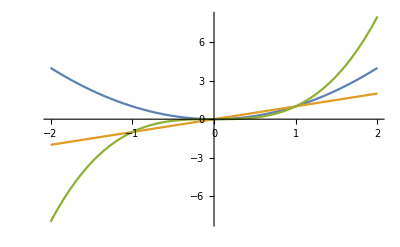

```mathematica
Plot[{x^2,x,x^3},{x,-2,2}]
```

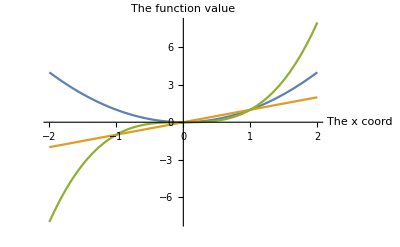

```mathematica
Plot[{x^2,x,x^3},{x,-2,2},AxesLabel-> {"The x coord", "The function value"}]
```

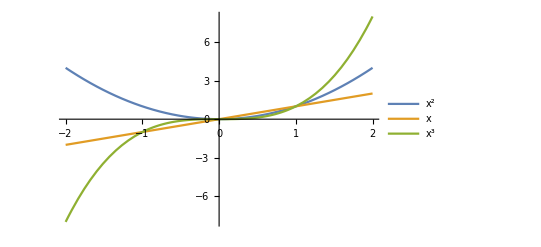

```mathematica
Plot[{x^2,x,x^3},{x,-2,2},PlotLegends->"Expressions"]
```

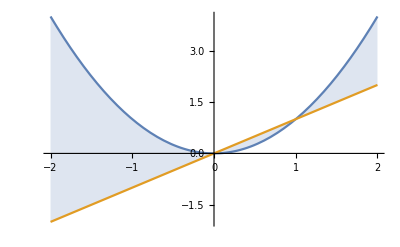

```mathematica
Plot[{x^2,x},{x,-2,2},Filling->{1->{2}}]
```

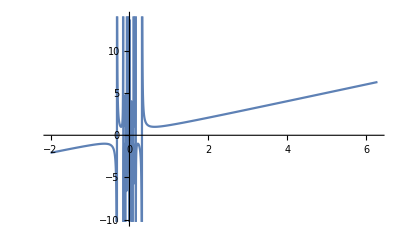

```mathematica
Plot[1/Sin[1/x],{x,-2,2*Pi}]
```

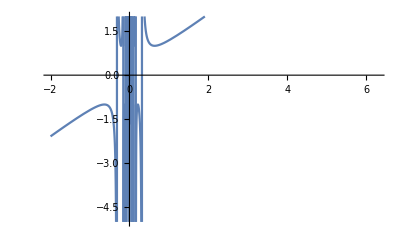

```mathematica
Plot[1/Sin[1/x],{x,-2,2*Pi},PlotRange->{-5,2}]
```

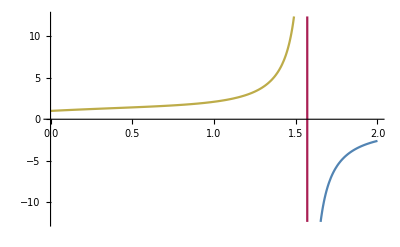

```mathematica
Plot[Cos[x]+Tan[x],{x,0,2},ColorFunction->"Rainbow"]
```

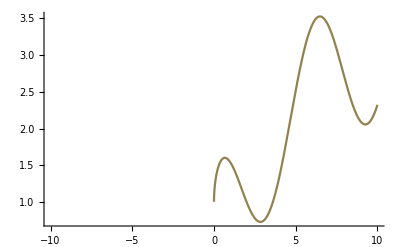

```mathematica
Plot[Cos[x]+Sqrt[x],{x,-10,10},ColorFunction->Function[{x,y},Hue[y]]]
```

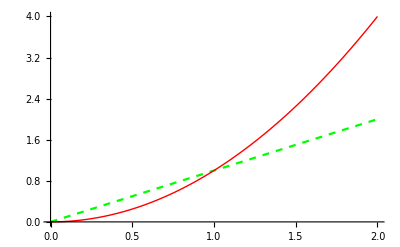

```mathematica
Plot[{x,x^2},{x,0,2},PlotStyle->{{Dashed,Green},{Thick,Red}}]
```

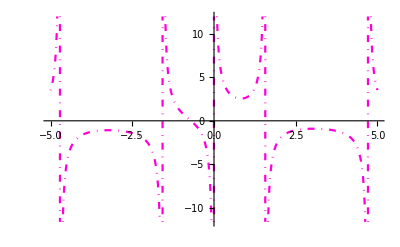

```mathematica
Plot[1/Cos[x]+1/Sinh[x],{x,-5,5},PlotStyle->Directive[RGBColor[1.,0.,0.85],DotDashed]]
```

```mathematica
Manipulate[Plot[x+x^2+a*x^3,{x,-2,2}],{a,-2,2}]
```

Show::gtype: Out is not a type of graphics. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Show/gtype",
ButtonNote->"Show::gtype"]

```mathematica
Manipulate[Plot[d+c*x+b*x^2+a*x^3,{x,-5,5}],{a,-5,5},{b,-5,5},{c,-5,5},{d,-5,5}]
```

```mathematica
Array[Prime[#] &, 20]
```

```mathematica
data1 ={2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

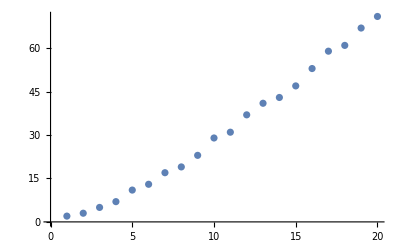

```mathematica
ListPlot[data1]
```

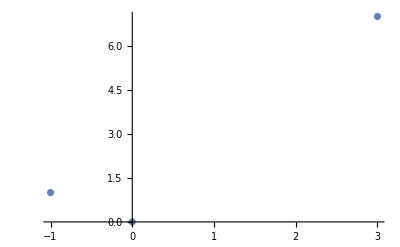

```mathematica
ListPlot[{{-1,1},{3,7},{0,0}}]
```

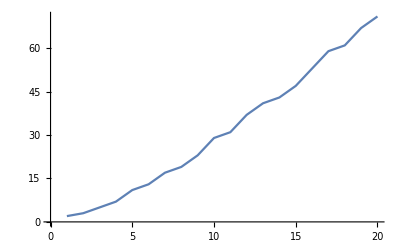

```mathematica
ListPlot[data1,Joined->True]
```

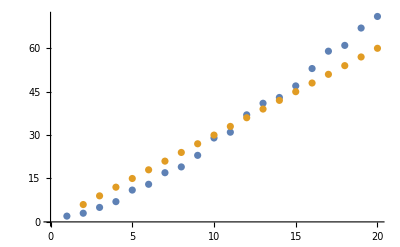

```mathematica
ListPlot[{data1,Table[{i,3*i},{i,2,20}]}]
```

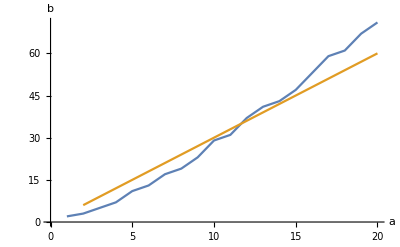

```mathematica
ListPlot[{data1,Table[{i,3*i},{i,2,20}]},Joined->True,AxesLabel->{"a","b"}]
```

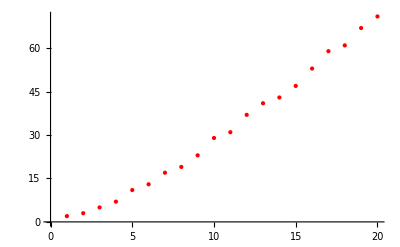

```mathematica
ListPlot[data1,PlotStyle->{Red,PointSize[Large]}]
```

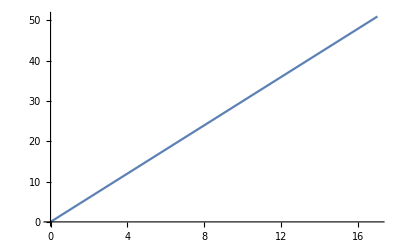

```mathematica
Plot[3*x,{x,0,17}]
```

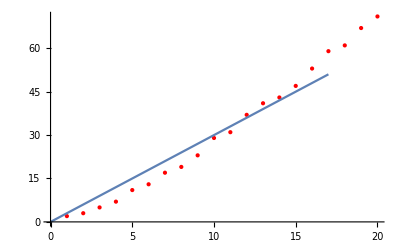

```mathematica
Show[ {ListPlot[data1,PlotStyle->{Red,PointSize[Large]}],Plot[3*x,{x,0,17}]}]
```

```mathematica
Plot3D[2^Sin[x]+2^Cos[y]-2^Sqrt[Sin[x]],{x,-2,2},{y,-2,2},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[func[myData[[i]],n,x],{x,0,2*Pi},{y,0,2*Pi},PlotRange->{-2,2},ColorFunction->"Rainbow"],{i,1,5,1},{n,.5,1.5},Initialization:> (func[dat_,n_,x_,y_]:=nSin[dat*x]+nCos[dat*y];myData={1,2,3,4,5})]
```

```mathematica
data1=Array[Prime[#] &,20]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
data2=Table[{i,data1[[i]]},{i,1,Length[data1]}]
```

{{1,2},{2,3},{3,5},{4,7},{5,11},{6,13},{7,17},{8,19},{9,23},{10,29},{11,31},{12,37},{13,41},{14,43},{15,47},{16,53},{17,59},{18,61},{19,67},{20,71}}

```mathematica
Fit[data2,{1,x},x]
```

-7.67368+3.77368 x

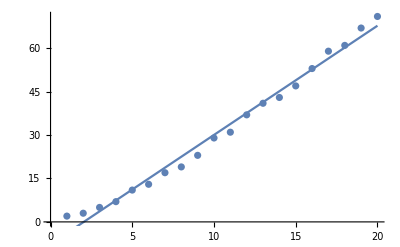

```mathematica
Show[{ListPlot[data2],Plot[-7.673684210526327+3.7736842105263184 x,{x,1,20}]}]
```

```mathematica
Fit[data2,{1,x,x^2,x^3,x^4},x]
```

1.15506+0.364087 x+0.355653 x^2-0.0153856 x^3+0.000272912 x^4

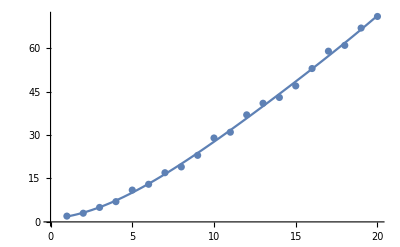

```mathematica
Show[{ListPlot[data2],Plot[1.1550567595460084+0.36408718018789343 x+0.3556525767161518 x^2-0.015385633831925814 x^3+0.0002729118483257762 x^4,{x,1,20}]}]
```

```mathematica
FindFit[Table[Prime[x],{x,20}],Exp[AA*y+BB],{AA,BB},y]
```

{AA→0.112575,BB→2.10152}

```mathematica
ReplaceAll[Exp[AA*y+BB],{AA->0.11257527366616696,BB->2.101519499121107}]
```

ⅇ^(2.10152+0.112575 y)

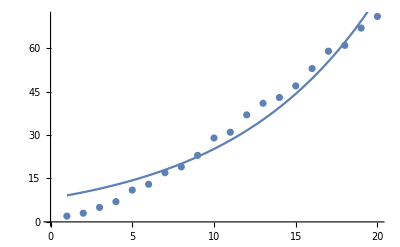

{}

General::ivar: 0. is not a valid variable.

```mathematica
Show[{ListPlot[data2],Plot[Exp[2.10152+0.112575x],{x,1,20}]}]
```